```mathematica
(*This mathematica notebook implements the delta-method calculations which estimate the variance of the coherence and phase estimators by writing the cross spectrum and power spectra as quadratic forms *)

$Assumptions = A > 0 &&ϕ>=0 && θ >= 0 && f >= 0 && f <= 1 && θ < 2 * π && ϕ < 2 * π && Y > 0 && B > 0 && P > 0&&H>0 && J>0 &&ϕ∈Reals&&T>=0&&Pa>0&&Pb>0 && γ>0 && γ < 1&&Px >0 && Py>0;
G[x_]:=1/Sqrt[2π] Exp[-x^2/2];
F1 = Sqrt[Px/2] * (A + ⅈ B);
F2 = T* F1 *ⅇ^(ⅈ*ϕ)+  (H + ⅈ J)*norm;
P1 = F1 * Conjugate[F1]//ComplexExpand//FullSimplify;
P2 = F2 * Conjugate[F2]//ComplexExpand//FullSimplify;
CC = Conjugate[F1] * F2//ComplexExpand//FullSimplify;
Gr = Re[CC]//ComplexExpand//FullSimplify;
Gi = Im[CC]//ComplexExpand//FullSimplify;
fullbounds = {{A,-Infinity,Infinity},{B,-Infinity,Infinity},{H,-Infinity,Infinity},{J,-Infinity,Infinity}};
norm = Sqrt[(Py - Px T^2)/2];
T = Sqrt[(Py*γ^2)/Px];
```

```mathematica
(*Define the mixing matrices*)
Avec = {A,B,H,J};
mvec = {0,0,0,0};
Σ = IdentityMatrix[4];
Γr =Sqrt[Px*Py]/4 ({{2γ Cos[ϕ], 0, √(1- γ^2), 0}, {0, 2 γ Cos[ϕ], 0, √(1- γ^2)}, {√(1- γ^2), 0, 0, 0}, {0, √(1- γ^2), 0, 0}});
Γi = Sqrt[Px*Py]/4 ({{2γ Sin[ϕ], 0, 0, √(1- γ^2)}, {0, 2 γ Sin[ϕ], -√(1- γ^2), 0}, {0, -√(1- γ^2), 0, 0}, {√(1- γ^2), 0, 0, 0}});
Γ1 = Px/2 ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Γ2 = Py/4({{2 γ^2, 0, 2 γ √(1-γ^2) Cos[ϕ], Sin[ϕ]2 γ √(1-γ^2)}, {0, 2 γ^2, -Sin[ϕ]2 γ √(1-γ^2), 2 γ √(1-γ^2) Cos[ϕ]}, {2 γ √(1-γ^2)Cos[ϕ], -Sin[ϕ]2 γ √(1-γ^2), 2-2 γ^2, 0}, {Sin[ϕ]2 γ √(1-γ^2), 2 γ √(1-γ^2) Cos[ϕ], 0, 2-2 γ^2}});
```

```mathematica
(*Check our matrices*)
quadGr = Avec.Γr.Transpose[Avec]//FullSimplify;
quadGi = Avec.Γi.Transpose[Avec]//FullSimplify;
quadP1 = Avec.Γ1.Transpose[Avec]//FullSimplify;
quadP2 = Avec.Γ2.Transpose[Avec]//FullSimplify;
quadGr==Gr//ComplexExpand//FullSimplify &&quadGi==Gi//ComplexExpand//FullSimplify&&quadP1==P1//FullSimplify&&quadP2==P2//FullSimplify
```

True

```mathematica
(*Calculate expectations*)
EGr = Tr[Σ.Γr] + Transpose[mvec] . Γr . mvec//FullSimplify;
EGi = Tr[Σ.Γi] + Transpose[mvec] . Γi . mvec//FullSimplify;
EP1 = Tr[Σ.Γ1] + Transpose[mvec] . Γ1 . mvec//FullSimplify;
EP2 = Tr[Σ.Γ2] + Transpose[mvec] . Γ2 . mvec//FullSimplify;
```

```mathematica
(*Calculate Variances*)
VarGr = 2*Tr[Σ.Γr.Σ.Γr]+4*mvec.Γr.Σ.Γr.Transpose[mvec]//FullSimplify;
VarGi = 2*Tr[Σ.Γi.Σ.Γi]+4*mvec.Γi.Σ.Γi.Transpose[mvec]//FullSimplify;
VarP1 = 2*Tr[Σ.Γ1.Σ.Γ1]+4*mvec.Γ1.Σ.Γ1.Transpose[mvec]//FullSimplify;
VarP2 = 2*Tr[Σ.Γ2.Σ.Γ2]+4*mvec.Γ2.Σ.Γ2.Transpose[mvec]//FullSimplify;
```

```mathematica
(*Calculate Covariances*)
CovGrGi = 2*Tr[Σ.Γr.Σ.Γi]+4*mvec.Γr.Σ.Γi.Transpose[mvec]//FullSimplify;
CovGrP1 = 2*Tr[Σ.Γr.Σ.Γ1]+4*mvec.Γr.Σ.Γ1.Transpose[mvec]//FullSimplify;
CovGrP2 = 2*Tr[Σ.Γr.Σ.Γ2]+4*mvec.Γr.Σ.Γ2.Transpose[mvec]//FullSimplify;
CovGiP1 = 2*Tr[Σ.Γi.Σ.Γ1]+4*mvec.Γi.Σ.Γ1.Transpose[mvec]//FullSimplify;
CovGiP2 = 2*Tr[Σ.Γi.Σ.Γ2]+4*mvec.Γi.Σ.Γ2.Transpose[mvec]//FullSimplify;
CovP1P2 = 2*Tr[Σ.Γ1.Σ.Γ2]+4*mvec.Γ1.Σ.Γ2.Transpose[mvec]//FullSimplify;
Covar = ({{VarGr, CovGrGi, CovGrP1, CovGrP2}, {CovGrGi, VarGi, CovGiP1, CovGiP2}, {CovGrP1, CovGiP1, VarP1, CovP1P2}, {CovGrP2, CovGiP2, CovP1P2, VarP2}})//FullSimplify;
```

```mathematica
(*Check that covariance is symmetric and positive semidefinite*)
SymmetricMatrixQ[Covar];
M1 = Covar[[1,1]];
M2 = Covar[[1;;2,1;;2]];
M3 = Covar[[1;;3,1;;3]];
M4=Covar;
Det[M2]>0 && Det[M3]>0 && Det[M4]>0 && M1 >0//FullSimplify
```

True

```mathematica
(*Now that we have the covariance matrix, we can apply the delta method and estimate the variance of γ*)
gradγ = Grad[(gr^2 +gi^2)/(p1*p2),{gr,gi,p1,p2}];
gradγevaluated = gradγ/.{gr->EGr,gi->EGi,p1->EP1,p2->EP2};
varγ = 1/n Transpose[gradγevaluated ].Covar.gradγevaluated//FullSimplify
```

(2 γ^2 (-1+γ^2)^2)/n

```mathematica
(*Variance of phi*)
(******************************************)
```

```mathematica
phifunc = ArcTan[gi,gr];
gradϕeval = Grad[phifunc,{gr,gi}]/.{gr->EGr,gi->EGi};
CovarGonly = {{VarGr,CovGrGi},{CovGrGi,VarGi}};
```

```mathematica
varphi = 1/n Transpose[gradϕeval].CovarGonly.gradϕeval//FullSimplify
```

-(-1+γ^2)/(2 n γ^2)

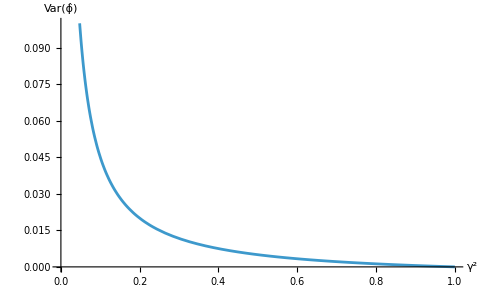

```mathematica
Plot[-(-1+γ2)/(2 n γ2)/.n->100,{γ2,0,1},AxesLabel->{Style["γ^2",Bold,16],Style["Var(ϕ̂)",Bold,16]},PlotRange->{0,.1}]
```

```mathematica
(*Variance between the phase lag and coherence and the forms*)
```

```mathematica
(*Gradients at true values*)gradGamma2={2γ Cos[ϕ]/Sqrt[Px*Py],2γ Sin[ϕ]/Sqrt[Px*Py],-γ^2/Px,-γ^2/Py};
gradPhi={-Sin[ϕ]/(γ Sqrt[Px*Py]),Cos[ϕ]/(γ Sqrt[Px*Py]),0,0};
```

```mathematica
(*Covariance between γ.b2 and φ*)
CovGammaPhi=Transpose[gradGamma2].Covar.gradPhi/n//FullSimplify
```

0

```mathematica
(*Covariances with base quantities*)
CovGammaGr=Transpose[gradGamma2].Covar[[All,1]]/n//FullSimplify;
CovGammaGi=Transpose[gradGamma2].Covar[[All,2]]/n//FullSimplify;
CovGammaP1 = Transpose[gradGamma2].Covar[[All,3]]/n //FullSimplify;
CovGammaP2 = Transpose[gradGamma2].Covar[[All,4]]/n //FullSimplify;
CovPhiGr=Transpose[gradPhi].Covar[[All,1]]/n//FullSimplify;
CovPhiGi=Transpose[gradPhi].Covar[[All,2]]/n//FullSimplify;
CovPhiP1 = Transpose[gradPhi].Covar[[All,3]]/n//FullSimplify;
CovPhiP2 = Transpose[gradPhi].Covar[[All,4]]/n//FullSimplify;
```

```mathematica
fullcovar = ({{VarGr, CovGrGi, CovGrP1, CovGrP2, CovGammaGr, CovPhiGr}, {CovGrGi, VarGi, CovGiP1, CovGiP2, CovGammaGi, CovPhiGi}, {CovGrP1, CovGiP1, VarP1, CovP1P2, CovGammaP1, CovPhiP1}, {CovGrP2, CovGiP2, CovP1P2, VarP2, CovGammaP2, CovPhiP2}, {CovGammaGr, CovGammaGi, CovGammaP1, CovGammaP2, varγ, CovGammaPhi}, {CovPhiGr, CovPhiGi, CovPhiP1, CovPhiP2, CovGammaPhi, varphi}});
```

```mathematica
SymmetricMatrixQ[fullcovar]
```

True